```mathematica
Clear [p1,p2,p3,p];
```

```mathematica
p1={x1,y1};
p2={x2,y2};
p3={x3,y3};
p={x,y};
```

```mathematica
pol1=(p1-p2).(p1-p2)==l1^2;
pol2=(p2-p3).(p2-p3)==l2^2;
pol3=(p3-p1).(p3-p1)==l3^2;
polys={pol1,pol2,pol3}   (*не понял как тут теорему косинусов применить, но так вроде правильно получается*)
```

{(x1-x2)^2+(y1-y2)^2==l1^2,(x2-x3)^2+(y2-y3)^2==l2^2,(-x1+x3)^2+(-y1+y3)^2==l3^2}

```mathematica
polys1={EuclideanDistance[p2,p]==R,EuclideanDistance[p3,p]==R,EuclideanDistance[p1,p]==R}
```

{√(Abs[-x+x2]^2+Abs[-y+y2]^2)==R,√(Abs[-x+x3]^2+Abs[-y+y3]^2)==R,√(Abs[-x+x1]^2+Abs[-y+y1]^2)==R}

```mathematica
polys2 = Last[Cross[Flatten[{p1-p2,0}],Flatten[{p3-p2,0}]]]==2s
```

x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3==2 s

```mathematica
polys0=Flatten[{polys,polys1,polys2}]
```

{(x1-x2)^2+(y1-y2)^2==l1^2,(x2-x3)^2+(y2-y3)^2==l2^2,(-x1+x3)^2+(-y1+y3)^2==l3^2,√(Abs[-x+x2]^2+Abs[-y+y2]^2)==R,√(Abs[-x+x3]^2+Abs[-y+y3]^2)==R,√(Abs[-x+x1]^2+Abs[-y+y1]^2)==R,x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3==2 s}

```mathematica
Simplify[GroebnerBasis[Simplify[polys0,Assumptions->{p1>0,p2>0,p3>0,p>0}],{l1,l2,l3,R,s},{x1,x2,x3,y1,y2,y3,x,y}]]
```

{l2^8 l3^4-2 l2^6 l3^6-32 l2^2 l3^4 R^2 s^2+256 R^4 s^4+l2^4 (l3^8+16 l3^4 s^2-32 l3^2 R^2 s^2),l2^6 l3^2-2 l2^4 l3^4+16 (l1^2-2 l3^2) R^2 s^2+l2^2 (l3^6+16 l3^2 s^2-32 R^2 s^2),l1^2 l2^2 l3^2-16 R^2 s^2,l1^4+l2^4-2 l2^2 l3^2+l3^4-2 l1^2 (l2^2+l3^2)+16 s^2}

```mathematica
Simplify[(16(pe(pe-l1)(pe-l2)(pe-l3))/.{pe->(l1+l2+l3)/2})+(l1^4+l2^4-2 l2^2 l3^2+l3^4-2 l1^2 (l2^2+l3^2))] (*проверка Герона, вычисление R - это предпоследний элемент %*)
```

0

```mathematica
l1=1;
l2=2;
polys = {l1 c1+l2(c2 c1-s2 s1)==a,l1 s1+l2(c2 s1+s2 c1)==b,c1^2+s1^2==1,c2^2+s2^2==1}
```

{c1+2 (c1 c2-s1 s2)==a,s1+2 (c2 s1+c1 s2)==b,c1^2+s1^2==1,c2^2+s2^2==1}

```mathematica
basis=Simplify[GroebnerBasis[polys,{c2,s2,c1,s1}]]
```

{a^4+(-3+b^2-2 b s1)^2+2 a^2 (-5+b^2-2 b s1+2 s1^2),3-a^2-b^2+2 a c1+2 b s1,-a^3-2 c1 (-3+b^2-2 b s1)-a (-7+b^2-2 b s1+4 s1^2),-1+c1^2+s1^2,-b c1+a s1+2 s2,5-a^2-b^2+4 c2}

```mathematica
Solve[basis[[1]]==0,s1]
```

{{s1→(-3 b+a^2 b+b^3-√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4))/(2 (a^2+b^2))},{s1→(-3 b+a^2 b+b^3+√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4))/(2 (a^2+b^2))}}

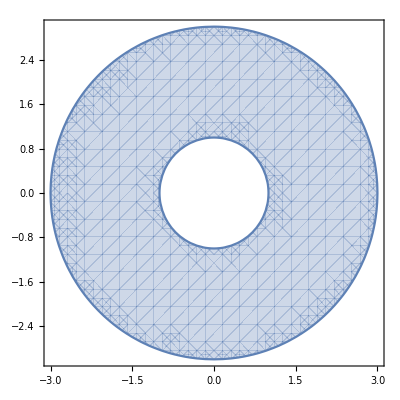

```mathematica
reg=RegionPlot[(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4)>=0,{a,-3,3},{b,-3,3}] (*под корнем больше равно нуля*)
```

```mathematica
(*так же бы выглядело (1,2->2,1)*)
```

```mathematica
sin1=First[Solve[basis[[1]]==0,s1]]
cos1=Solve[(basis[[2]]/.sin1)==0,c1]
sin2=Solve[(basis[[5]]/.Flatten[{sin1,cos1}])==0,s2]
cos2=Solve[(basis[[6]]/.Flatten[{sin1,cos1,sin2}])==0,c2]
```

{s1→(-3 b+a^2 b+b^3-√(-9 a^2+10 a^4-a^6+10 a^2 b^2-2 a^4 b^2-a^2 b^4))/(2 (a^2+b^2))}

{{c1→(-3 a^2+a^4+a^2 b^2+b √(-a^2 (9-10 a^2+a^4-10 b^2+2 a^2 b^2+b^4)))/(2 a (a^2+b^2))}}

{{s2→(√(-a^2 (9-10 a^2+a^4-10 b^2+2 a^2 b^2+b^4)))/(4 a)}}

{{c2→1/4 (-5+a^2+b^2)}}

```mathematica
Manipulate[ListPlot[{{0,0},Flatten[{(c1/.cos1),(s1/.sin1)}],{a,b}}/.{a->a1,b->b1},Joined->True,PlotRange->{{-3,3},{-3,3}},AspectRatio->1,PlotStyle->Red],{a1,-3,3},{b1,-3,3}]
```

ReplaceAll::reps: {cos1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {sin1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.